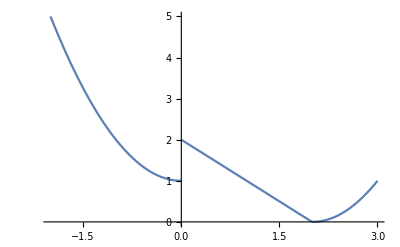

```mathematica
f[x_]:=Piecewise[{{1+x^2,x≤0},{2-x,0<x&&x≤2},{(x-2)^2,x>2}}]
Plot[f[x],{x,-2,3}]
```

{{x→-1.32472},{x→0.662359-0.56228 ⅈ},{x→0.662359+0.56228 ⅈ}}

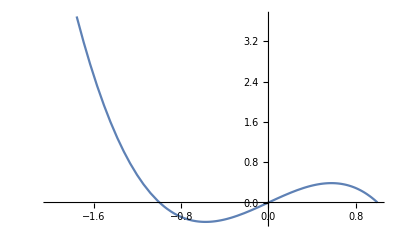

```mathematica
f[x_]:=x-x^3
Solve[f[x]==1,{x}]//N
Plot[f[x], {x,-2,1}]
```

```mathematica
Solve[4c+4==8-2c,c]
```

{{c→2/3}}

```mathematica
f[x_]:=2/3 x^2+2x
g[x_]:=x^3-2/3 x
```

```mathematica
f[2]
g[2]
```

20/3

20/3

```mathematica
Simplify[(x^4-1)/(x-1)]//Factor//TraditionalForm
```

(x+1) (x^2+1)